# VYA - Přednášky

## 1. Přednáška

### Tři důležité příkazy

```mathematica
Quiet[Remove["Global`*"]];
```

Vymaže předchozí definice

```mathematica
$HistoryLength = 2;
```

Omezuje paměť jádra, opatření proti přetečení paměti

```mathematica
SetDirectory[NotebookDirectory[]];
```

SetDir. ~ zavede místo nalezené NotebookDir. ~ cesta k lokaci. jako defaultní adresář

### Struktura výrazu, základy syntaxu

? ~ Help, fomát ? + symbol

```mathematica
?=
```

```mathematica
Vyraz = x+y + Sin[x^2+2*x*y+3]
```

x+y+Sin[3+x^2+2 x y]

```mathematica
Vyraz = x + y + Sin[x^2 + 2xy +3];
```

; ~ Input bez výstupu

```mathematica
?;
```

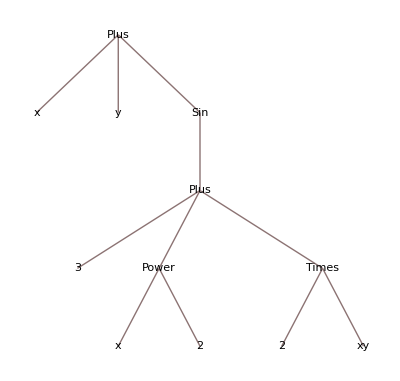

```mathematica
TreeForm[Vyraz]
```

```mathematica
?TreeForm
```

```mathematica
FullForm[Vyraz]
```

Plus[x,y,Sin[Plus[3,Power[x,2],Times[2,xy]]]]

```mathematica
Plus[x,y,Sin[Plus[3,Power[x,2],Times[2,xy]]]]
```

x+y+Sin[3+x^2+2 xy]

```mathematica
?FullForm
```

```mathematica
Head[Vyraz]
```

Plus

```mathematica
?Head
```

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
?Attributes
```

### List

```mathematica
ListTree = {1, {2, 3}, {0,{ A, B}}}
```

{1,{2,3},{0,{A,B}}}

{1,{2,3},{0,{A,B}}}

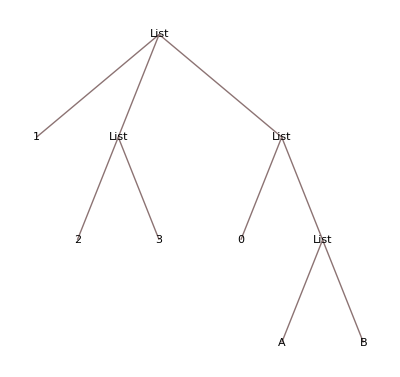

```mathematica
{1,{2,3},{0,{A,B}}}
TreeForm[ListTree]
```

```mathematica
ListTree[[1]]
ListTree[[2]]
ListTree[[3]]
ListTree[[-1]]
```

1

{2,3}

{0,{A,B}}

{0,{A,B}}

```mathematica
ListTree[[0]]
```

List

```mathematica
ListTree[[3, 2, 1]]
```

A

```mathematica
ListTree[[-1,-1,-1]]=C;
ListTree
```

{1,{2,3},{0,{A,C}}}

```mathematica
?Part
```

```mathematica
Length[ListTree]
```

3

```mathematica
?Length
```

```mathematica
Head[ListTree]
ListTree[[0]]
```

List

List

```mathematica
First[ListTree]
ListTree[[1]]
```

1

1

```mathematica
Last[ListTree]
ListTree[[-1]]
```

{0,{A,C}}

{0,{A,C}}

Volání výrazů

```mathematica
{Sin[x], Sin@x, x//Sin}
```

{Sin[x],Sin[x],Sin[x]}

### Souvislost listu a výrazu

```mathematica
TreeForm[Vyraz]
```

-Graphics-

```mathematica
Vyraz[[0]]
Head[Vyraz]
```

Plus

Plus

```mathematica
Vyraz[[1]]
First[Vyraz]
```

x

x

```mathematica
Vyraz[[2]]
Vyraz[[3]]
Vyraz[[-1]]
Last[Vyraz]
```

y

Sin[3+x^2+2 xy]

Sin[3+x^2+2 xy]

Sin[3+x^2+2 xy]

```mathematica
Vyraz[[3, 1]]
```

3+x^2+2 xy

```mathematica
Vyraz[[3, 1, 1]]
Vyraz[[3, 1, 2]]
Vyraz[[3, 1, 2, 1]]
Vyraz[[3, 1, 2, 2]]
Vyraz[[3, 1, 3]]
Vyraz[[3, 1, 3, 1]]
```

3

x^2

x

2

2 xy

2

### Pravidla a programování pomocí nich

```mathematica
x^2 /. x ->2
ReplaceAll[x^2,Rule[x,2]]
```

4

4

/.	=	ReplaceAll
→	=	Rule

```mathematica
?ReplaceAll
```

```mathematica
?Rule
```

```mathematica
x^2 + y /. {x-> E, y ->Pi}
```

ⅇ^2+π

```mathematica
x^2 + y /. {x-> E, y ->Pi, x->C}
```

ⅇ^2+π

```mathematica
1/(I*w*c) /. {c -> 10nF, nF -> 10^-9}
1/(I*w*c) /. {c -> 10nF}
```

-ⅈ/(10 nF w)

-ⅈ/(10 nF w)

```mathematica
1/(I*w*c) //. {c -> 10nF, nF -> 10^-9}
```

-(100000000 ⅈ)/w

//.	=	ReplaceRepeated

```mathematica
?ReplaceRepeated
```

```mathematica
(*x //. {x-> y+x, y -> x}*)
```

```mathematica
x^2 /. {{x -> 2}, {x -> 3}, {x -> 4}}
```

{4,9,16}

==	=	Equal

```mathematica
?Equal
```

```mathematica
Equal[lhs, rhs]
lhs == rhs
```

lhs==rhs

lhs==rhs

```mathematica
{1 == 1, 1 == 2, Equal[1,1], Equal[1,2]}
```

{True,False,True,False}

Pro řešení kořenů rovnice

```mathematica
Rovnice = x^3 + (2 + I)*x^2 + 2I*x + 14 == 0
```

14+2 ⅈ x+(2+ⅈ) x^2+x^3==0

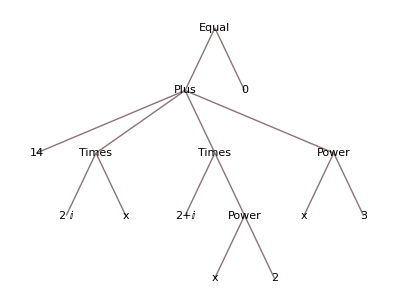

```mathematica
TreeForm[Rovnice]
```

```mathematica
lhs = Rovnice[[1]]
rhs = Rovnice[[2]]
```

14+2 ⅈ x+(2+ⅈ) x^2+x^3

0

```mathematica
Reseni = Solve[Rovnice]
```

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

```mathematica
Rovnice = x^3 + (2 + I)*x^2 + 2I*x + 14. == 0
```

14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0

```mathematica
14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0
Reseni = Solve[Rovnice]
x /. Solve[Rovnice]
```

14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

{Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176,Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709,Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}

```mathematica
x1 = x /. Reseni[[1]]
x2 = x /. Reseni[[2]]
x3 = x /. Reseni[[3]]
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176

Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469

```mathematica
Vysledek = x1 + 2*x2
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
FormVysledku = a + 2*b;
FormVysledku /. {a -> x1, b -> x2}
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
Print["x1 + 2*x2 = ", Vysledek]
(x /. Reseni) . {1, 2, 0}
```

x1 + 2*x2 = Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
Expres = y - x /. {{x -> 2}, {x -> 3}, {x -> 4}}
Expres /. {List -> Times}
(Expres /. {List -> Times}) /. {y -> x}
Expand[(Expres /. {List -> Times}) /. {y -> x}]
0 == Expand[(Expres /. {List -> Times}) /. {y -> x}]
Reseni = Solve[0 == Expand[(Expres /. {List -> Times}) /. {y -> x}]]
```

{-2+y,-3+y,-4+y}

(-4+y) (-3+y) (-2+y)

(-4+x) (-3+x) (-2+x)

-24+26 x-9 x^2+x^3

0==-24+26 x-9 x^2+x^3

{{x→2},{x→3},{x→4}}

```mathematica
x1 = x /. Reseni[[1]];
x2 = x /. Reseni[[2]];
x3 = x /. Reseni[[3]];
Print["x1 = ", x1]
Print["x2 = ", x2]
Print["x3 = ", x3]
```

x1 = 2

x2 = 3

x3 = 4

```mathematica
Reseni[[1]]
Reseni[[1,1]]
Reseni[[1,1,1]]
Reseni[[1,1,2]]
xRes = {Reseni[[1,1,2]], Reseni[[2,1,2]], Reseni[[3,1,2]]}
```

{x→2}

x→2

x

2

{2,3,4}

```mathematica
Range[100]
Range[100] /. List -> Plus
Range[100] /. List -> Times
N[Range[100] /. List -> Times]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

5050

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

9.33262×10^157